# Arbitrarily Space uneven nesting of elements

```mathematica
Quit[]
```

## Import package

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<ArbitrarilySpace`
```

## Demo Data

```mathematica
complexList={1,1,1,{2,2,{3,3,{4,4,{5,{6,{7,7}},4}},3},2},1,1,1};
```

## Arbitrarily Space

```mathematica
as= ArbitrarilySpace[complexList];
Join[{{"element","absolute index","level","relative index", "last in level instance","size","post spacing", "aggregation","color"}},as]//TableForm
```

element | absolute index | level | relative index | last in level instance | size | post spacing | aggregation | color
1 | 1 | 1 | 1 | False | 1 | 1 | 0 | RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]
1 | 2 | 1 | 2 | False | 1 | 1 | 2 | RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]
1 | 3 | 1 | 3 | False | 1 | 1 | 4 | RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]
2 | 4 | 2 | 1 | False | 1 | 1/2 | 6 | RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997]
2 | 5 | 2 | 2 | False | 1 | 1/2 | 15/2 | RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997]
3 | 6 | 3 | 1 | False | 1 | 1/3 | 9 | RGBColor[0.25554042857142856, 0.25139634285714285, 0.767193]
3 | 7 | 3 | 2 | False | 1 | 1/3 | 31/3 | RGBColor[0.25554042857142856, 0.25139634285714285, 0.767193]
4 | 8 | 4 | 1 | False | 1 | 1/4 | 35/3 | RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858]
4 | 9 | 4 | 2 | False | 1 | 1/4 | 155/12 | RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858]
5 | 10 | 5 | 1 | False | 1 | 1/5 | 85/6 | RGBColor[0.27562585714285714, 0.6141225714285714, 0.9531118571428572]
6 | 11 | 6 | 1 | False | 1 | 1/6 | 461/30 | RGBColor[0.4922118571428571, 0.7744759999999999, 0.9840624285714286]
7 | 12 | 7 | 1 | False | 1 | 1/7 | 248/15 | RGBColor[0.772061, 0.92462, 0.998703]
7 | 13 | 7 | 2 | True | 1 | 1/6 | 1856/105 | RGBColor[0.772061, 0.92462, 0.998703]
4 | 14 | 5 | 3 | True | 1 | 1/4 | 1319/70 | RGBColor[0.27562585714285714, 0.6141225714285714, 0.9531118571428572]
3 | 15 | 3 | 4 | True | 1 | 1/2 | 2813/140 | RGBColor[0.25554042857142856, 0.25139634285714285, 0.767193]
2 | 16 | 2 | 4 | True | 1 | 1 | 3023/140 | RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997]
1 | 17 | 1 | 5 | False | 1 | 1 | 3303/140 | RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]
1 | 18 | 1 | 6 | False | 1 | 1 | 3583/140 | RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]
1 | 19 | 1 | 7 | True | 1 | 1 | 3863/140 | RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]

## How to use in practice?

The information from ArbitrarilySpace allows for visualizations with complex spacing depending on the data nest-schema of the user. Thus it is easy to use the values provided to move any elements over in either horizontal or vertical oriented charts.

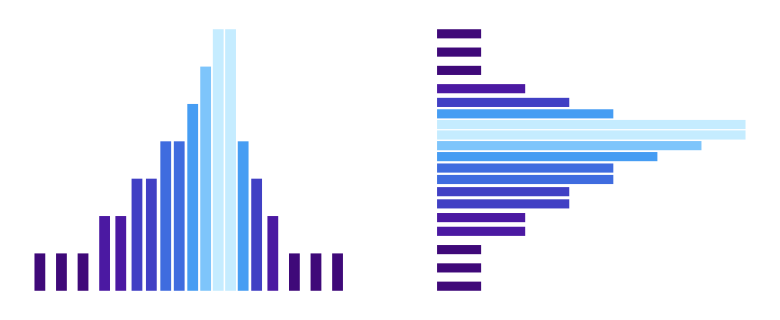

```mathematica
GraphicsRow[{
Graphics[ArbitrarilySpaceBarChart[as,True]],
Graphics[ArbitrarilySpaceBarChart[as,False]]
}]
```

## More complex charts?

Since ArbitrarilySpace traverse all elements with Head@element==List, how could one use this for charts like BoxWhiskerChart?
Simple. Do normal calculations needed for the chart, then wrap them with a head like BoxWhiskerValues[...].

```mathematica
Join[{
{
"el", "abs i", "level", "rel i", "lastQ"
}
},

ExtractListStructure[
{
BoxWhiskerValues["Q1"->25,"Q2"->50,"Q3"->75],
{
BoxWhiskerValues["Q1"->5,"Q2"->10,"Q3"->15],
BoxWhiskerValues["Q1"->2,"Q2"->5,"Q3"->7]
},
BoxWhiskerValues["Q1"->20,"Q2"->35,"Q3"->47],
BoxWhiskerValues["Q1"->20,"Q2"->35,"Q3"->47]
},
"AtomQ"->MatchQ@_BoxWhiskerValues
]
]//TableForm
```

el | abs i | level | rel i | lastQ
BoxWhiskerValues[Q1→25,Q2→50,Q3→75] | 1 | 1 | 1 | True
BoxWhiskerValues[Q1→5,Q2→10,Q3→15] | 2 | 2 | 1 | True
BoxWhiskerValues[Q1→2,Q2→5,Q3→7] | 3 | 2 | 2 | True
BoxWhiskerValues[Q1→20,Q2→35,Q3→47] | 4 | 1 | 3 | True
BoxWhiskerValues[Q1→20,Q2→35,Q3→47] | 5 | 1 | 4 | True

## Break down: piece by piece analysis of code

### Extract List Structure

```mathematica
els=ExtractListStructure[{2,{{2,{2},{3,{4}}}}}];
els//TableForm
```

2 | 1 | 1 | 1 | False
2 | 2 | 3 | 1 | False
2 | 3 | 4 | 1 | True
3 | 4 | 4 | 1 | False
4 | 5 | 5 | 1 | True

### Position Tuples

```mathematica
pt=PositionTuples[els];
pt//TableForm
```

2 | 1 | 1 | 1 | False | 1 | 1 | 0 | RGBColor[0.27823319999999996, 0.04860976, 0.5418926000000001]
2 | 2 | 3 | 1 | False | 1 | 1/3 | 0 | RGBColor[0.2541886, 0.4613372, 0.8892074]
2 | 3 | 4 | 1 | True | 1 | 1/3 | 0 | RGBColor[0.3802722, 0.7144184, 0.9782062]
3 | 4 | 4 | 1 | False | 1 | 1/4 | 0 | RGBColor[0.3802722, 0.7144184, 0.9782062]
4 | 5 | 5 | 1 | True | 1 | 1/4 | 0 | RGBColor[0.772061, 0.92462, 0.998703]

### Aggregate over spacing values

```mathematica
as= ArbitrarilySpace[complexList]
```

{{1,1,1,1,False,1,1,0,RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]},{1,2,1,2,False,1,1,2,RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]},{1,3,1,3,False,1,1,4,RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]},{2,4,2,1,False,1,1/2,6,RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997]},{2,5,2,2,False,1,1/2,15/2,RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997]},{3,6,3,1,False,1,1/3,9,RGBColor[0.25554042857142856, 0.25139634285714285, 0.767193]},{3,7,3,2,False,1,1/3,31/3,RGBColor[0.25554042857142856, 0.25139634285714285, 0.767193]},{4,8,4,1,False,1,1/4,35/3,RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858]},{4,9,4,2,False,1,1/4,155/12,RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858]},{5,10,5,1,False,1,1/5,85/6,RGBColor[0.27562585714285714, 0.6141225714285714, 0.9531118571428572]},{6,11,6,1,False,1,1/6,461/30,RGBColor[0.4922118571428571, 0.7744759999999999, 0.9840624285714286]},{7,12,7,1,False,1,1/7,248/15,RGBColor[0.772061, 0.92462, 0.998703]},{7,13,7,2,True,1,1/6,1856/105,RGBColor[0.772061, 0.92462, 0.998703]},{4,14,5,3,True,1,1/4,1319/70,RGBColor[0.27562585714285714, 0.6141225714285714, 0.9531118571428572]},{3,15,3,4,True,1,1/2,2813/140,RGBColor[0.25554042857142856, 0.25139634285714285, 0.767193]},{2,16,2,4,True,1,1,3023/140,RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997]},{1,17,1,5,False,1,1,3303/140,RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]},{1,18,1,6,False,1,1,3583/140,RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]},{1,19,1,7,True,1,1,3863/140,RGBColor[0.24671228571428572, 0.03472125714285714, 0.4732578571428572]}}

## Example with Titanic

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}];
titanic[[1;;4]]
```

Dataset[<>]

```mathematica
survivedClasses=DeleteDuplicates[Normal[titanic[All,"survived"]]]
sexClasses=DeleteDuplicates[Normal[titanic[All,"survived"]]]
classClasses=DeleteDuplicates[Normal[titanic[All,"class"]]]

(*GroupBy[GroupBy[GroupBy[titanic,"survived"][[1]],"sex"][[1]],"class"]*)
```

{True,False}

{True,False}

{1st,2nd,3rd}

```mathematica
res=Table[
N@Mean[
DeleteMissing[
Normal[
GroupBy[
GroupBy[
GroupBy[titanic,
"survived"][[sr]]
,"sex"][[sx]],
"class"][[c]]
[All,"age"]
]]]
,{sr,Length@ survivedClasses},{sx,Length@ sexClasses},{c,Length@classClasses}];
```

```mathematica
cf[elementData_: {},level_Integer: 1,absoluteIndex_Integer: 1,relativeIndex_Integer: 1,maxDepth_: 1,colorGradient_:"DeepSeaColors"]:=ColorData[colorGradient][relativeIndex/3]


lsp[elementData_: {},level_Integer: 1,lastInLevelInstanceQ_: False,baseSpacerSize_:1]:=With[
{adjustedLevel=If[lastInLevelInstanceQ,level-1,level]},
If[lastInLevelInstanceQ, Return[level ]];
If[adjustedLevel==0,baseSpacerSize,baseSpacerSize/adjustedLevel ]
]

titanicAs=ArbitrarilySpace[
res,
LevelSizeFunction,
LevelSpacerFunction,
cf
];
Graphics[ArbitrarilySpaceBarChart[titanicAs,True],AspectRatio->1/2]
```

-Graphics-

```mathematica
titanicAs[[;;,5]]
```

{False,False,True,False,False,True,False,False,True,False,False,True}

```mathematica
titanicAs[[;;,-2]]//Differences
```

{4/3,4/3,4,4/3,4/3,4,4/3,4/3,4,4/3,4/3}

BarChart::ldata: {{{37.1094,26.7174,20.8333},{36.1698,17.4783,22.4576}},{{35.2,34.0909,23.4375},{43.6735,33.1037,26.7207}}} is not a valid dataset or list of datasets.

BarChart[{{{37.1094,26.7174,20.8333},{36.1698,17.4783,22.4576}},{{35.2,34.0909,23.4375},{43.6735,33.1037,26.7207}}}]

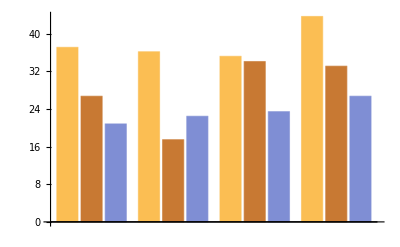

```mathematica
BarChart[res]
BarChart[Partition[Flatten[res],{3}]]
```

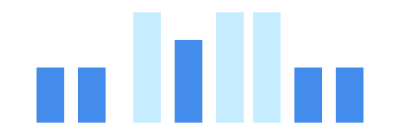

```mathematica
Graphics@ArbitrarilySpaceBarChart[ ArbitrarilySpace[
{
{2,2},
{{4},3,{4,4}},
{2,2}
}

]]
```

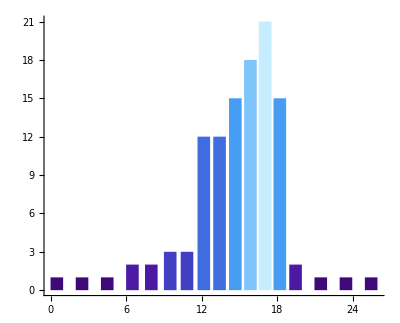

```mathematica
Graphics[ArbitrarilySpaceBarChart[as,True],Axes->{True,False} ]
```

```mathematica
Options[ExtractListStructure]={"AtomQ"->Not@*ListQ};
ExtractListStructure[ll_,OptionsPattern[]]:=
Block[
{
i=1,
prev=None
},
Reap[
MapIndexed[
Function[
If[
OptionValue["AtomQ"]@#,

If[
ListQ@prev,
prev[[5]]=False;
Sow@prev
];
prev={#,i++,Length@#2,Last@#2,None},

(*else*)
If[ListQ@prev,prev[[5]]=True;Sow@prev;prev=None]

];
#
],ll,All
]
][[2,1]]
];
```

```mathematica
InputForm[Hold[{1,1,1,{2,2,{3,3,{4,4,{5,{6,{7,7}},4}},3},2},1,1,1}]]
```

Hold[{1, 1, 1, {2, 2, {3, 3, {4, 4, {5, {6, {7, 7}}, 4}}, 3}, 2}, 1, 1, 1}]

```mathematica
complexList={1,1,1,{2,2,{3,3,{4,4,{5,{6,{7,7}},4}},3},2},1,1,1}
complexList//FullForm
```

{1,1,1,{2,2,{3,3,{4,4,{5,{6,{7,7}},4}},3},2},1,1,1}

List[1,1,1,List[2,2,List[3,3,List[4,4,List[5,List[6,List[7,7]],4]],3],2],1,1,1]

```mathematica
complexList
```

{1,1,1,{2,2,{3,3,{12,12,{15,{18,{21,21}},12}}},2},1,1,1}

```mathematica
ExtractListStructure[complexList]
```

1None

1{1,1,1,1,False}

1{1,2,1,2,False}

2{1,3,1,3,False}

2{2,4,2,1,False}

3{2,5,2,2,False}

3{3,6,3,1,False}

12{3,7,3,2,False}

12{12,8,4,1,False}

15{12,9,4,2,False}

18{15,10,5,1,False}

21{18,11,6,1,False}

21{21,12,7,1,False}

12None

2None

1None

1{1,16,1,5,False}

1{1,17,1,6,False}

{{1,1,1,1,False},{1,2,1,2,False},{1,3,1,3,False},{2,4,2,1,False},{2,5,2,2,False},{3,6,3,1,False},{3,7,3,2,False},{12,8,4,1,False},{12,9,4,2,False},{15,10,5,1,False},{18,11,6,1,False},{21,12,7,1,False},{21,13,7,2,True},{12,14,5,3,True},{2,15,2,4,True},{1,16,1,5,False},{1,17,1,6,False},{1,18,1,7,True}}